```mathematica
g = 9.81; (*acceleration due to gravity, m/s^2*)
M = 23; (*Mass of the moving platform,kg*)
m = 5; (*Mass of the bob at the and of the pendulum, kg*)
l = 4; (*length of the pendulum shaft, m*)
{q1,q2,q3,q4} = {1,1,1,1}; (*weights in the cost functional*)
r = 10; (*weights penelazing our control, acceleration*)
```

```mathematica
Import["https://upload.wikimedia.org/wikipedia/commons/thumb/0/00/Cart-pendulum.svg/1200px-Cart-pendulum.svg.png"]
```

-Graphics-

Above, we set up the parameters used in the inverse pendulum problem. The inverted pendulum is on a platform of mass M. The pendulum shaft is l long and is weightless, with a bob of mass m at the end.

```mathematica
A = {{0,1,0,0},{0,0,(m g)/M,0},{0,0,0,1},{0,0,(g(M+m))/(M*l),0}};
B = {{0},{1/M},{0},{1/(M l)}};
Q = DiagonalMatrix[{q1,q2,q3,q4}];
R = {{r}};
```

```mathematica
P= RiccatiSolve[{A,B},{Q,R}];
```

```mathematica
(A-B.(1/R).Bᵀ.P).{x,xp,θ,θp}
```

{0.+1. xp,0.013749 x+0.19947 xp-23.9371 θ-15.2243 θp,0.+1. θp,0.00343726 x+0.0498675 xp-3.53177 θ-3.80607 θp}

```mathematica
z0 = {-1,-1,0.1,-0.2}; (*Initial Conditions*)
```

```mathematica
s=NDSolve[{{x'[t],xp'[t],θ'[t],θp'[t]} == (A-B.(1/R).Bᵀ.P).{x[t],xp[t],θ[t],θp[t]},{x[0] ,xp[0] ,θ[0],θp[0]}==z0},{x[t],xp[t],θ[t],θp[t]},{t,0,60}][[1]]
```

{x[t]→InterpolatingFunction[…][t],xp[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],θp[t]→InterpolatingFunction[…][t]}

```mathematica
xpp[t_] = (-(1/R).Bᵀ.P).{x[t],xp[t],θ[t],θp[t]}/.s;
```

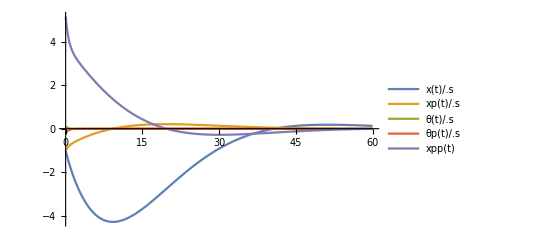

```mathematica
Plot[{x[t]/.s,xp[t]/.s,θ[t]/.s,θp[t]/.s,xpp[t]},{t,0,60},PlotRange->All,PlotLegends->"Expressions"]
```

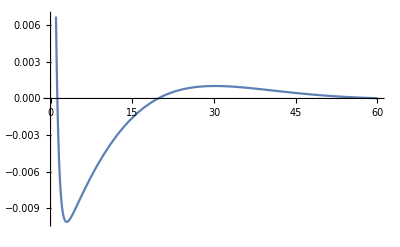

```mathematica
Plot[θ[t]/.s,{t,0,60}]
```

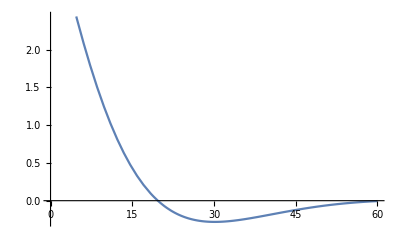

```mathematica
Plot[control[t],{t,0,60}]
```